Приложение Д.

```mathematica
Needs["Splines`"]
```

```mathematica
(*Разбор встроенной функции Spline*)
```

```mathematica
arr=Table[{Cos[t],Sin[t]},{t,0,2Pi-Pi/4,Pi/4}]
```

{{1,0},{1/(√2),1/(√2)},{0,1},{-1/(√2),1/(√2)},{-1,0},{-1/(√2),-1/(√2)},{0,-1},{1/(√2),-1/(√2)}}

```mathematica
points=ListPlot[arr,PlotRange->{{-1.2,1.2},{-1.2,1.2}}];
```

```mathematica
cubic=Graphics[Spline[arr,Cubic,SplineDots->Automatic],PlotRange->Automatic];
```

```mathematica
bezier=Graphics[Spline[arr,Bezier,SplineDots->Automatic],PlotRange->Automatic];
```

```mathematica
compositeBezier=Graphics[Spline[arr,CompositeBezier,SplineDots->Automatic],
PlotRange->Automatic];
```

```mathematica
(*Пример кубического сплайна*)
```

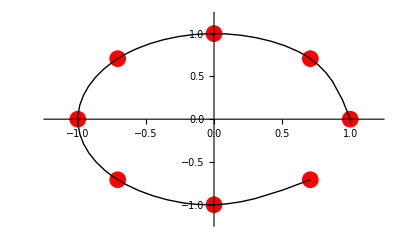

```mathematica
Show[points,cubic]
```

```mathematica
(*Пример сплайна Безье*)
```

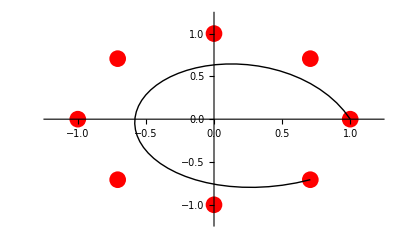

```mathematica
Show[points,bezier]
```

```mathematica
(*Пример составного сплайна Безье*)
```

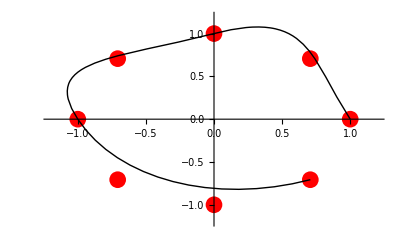

```mathematica
Show[points,compositeBezier]
```